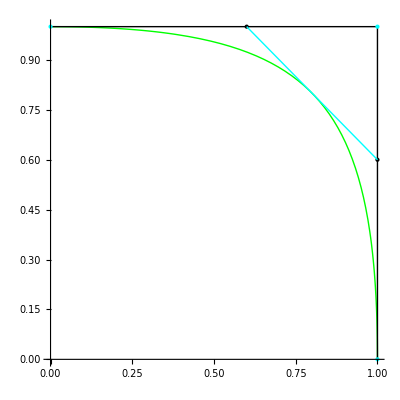

```mathematica
quadraticBez[b_,t_]:=Sum[b[[i+1]]*BernsteinBasis[2,i,t],{i,0,2}];
ratquadraticBez[b_,t_]:=(
val = Sum[b[[i+1]]*BernsteinBasis[2,i,t],{i,0,2}];
val=val/val[[3]];
Return[{val[[1]],val[[2]]}]
);
b2D = {{1,0,1}, {1,1,1}, {0,1,1}};
wts = {1.0, 2.0, 1.0};
p={0.8,0.8,1};
area=Area[Triangle[b2D]];
area0=Area[Triangle[{p,{1,1,1}, {0,1,1}}]];
area1=Area[Triangle[{{1,0,1}, p,{0,1,1}}]];
area2=Area[Triangle[{{1,0,1}, {1,1,1},p}]];
τ0=area0/area;
τ1=area1/area;
τ2=area2/area;
wts[[2]]=τ1/(2*Sqrt[τ0*τ2]);
b3D=b2D = {{1,0,1}, {1,1,1}, {0,1,1}};
b2d={{1,0}, {1,1}, {0,1}};
Do[b3D[[i]] = b2D[[i]]*wts[[i]], {i,1,3}];
wtpts1=(b2D[[1]]+wts[[2]]*b2D[[2]])/(1.0+wts[[2]]);
wtpts2=(b2D[[3]]+wts[[2]]*b2D[[2]])/(1.0+wts[[2]]);
wtpts12d={wtpts1[[1]],wtpts1[[2]]};
wtpts22d={wtpts2[[1]],wtpts2[[2]]};



curve2D = ParametricPlot[ratquadraticBez[b3D,t],{t,0,1},PlotStyle->{Thick, Green}];

polygon2D = Graphics[{Thick,Line[b2d]}];
points2D = Graphics[{Cyan,PointSize[Large],Point[b2d]}];
wtpts = Graphics[{PointSize[Large],Point[{wtpts12d,wtpts22d}]}];
wtpntLine = Graphics[{Thick,Cyan,Line[{wtpts12d, wtpts22d}]}];

(*curve3D = ParametricPlot3D[quadraticBez[b3D,t],{t,0,1},PlotStyle->{Thick, Red},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}}, Boxed->False];
polygon3D=Graphics3D[Line[b3D]];
points3D = Graphics3D[{PointSize[Large],Point[b3D]}];

(* t=0.5 line thru origin *)
line2origin = Graphics3D[{Thick,Magenta,Line[{ratquadraticBez[b3D,0.5],quadraticBez[b3D,0.5], {0,0,0}}]}];
 

pointOrigin = Graphics3D[{Black,PointSize[0.05],Point[{0,0,0}]}];*)

Show[{curve2D, polygon2D, points2D,wtpts,wtpntLine}, PlotRange->All]
```